```mathematica
<<"Dynamica_1011.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
projectHomeDir="./";
lineThickness=0.012;
legendThickness=lineThickness*20;
labelSize=20;
tickSize=15;
legendSize=15;
textSize=20;
colours=ColorData[97,"ColorList"];
```

### Cross-inhibition Model with Zealots

```mathematica
sysCI2EqZealotSym=DynamicalSystem[{
dA(1-A-B-z)-aA A+rA(A+z/2)(1-A-B-z)-bB A/q(B+z/2),
dB/q(1-A-B-z)-aB B+rB/q(B+z/2)(1-A-B-z)-bA B(A+z/2)},
{{A,-0.01,1+0.01},{B,-0.01,1+0.01}},
{{aA,0,10},{aB,0,10},{bA,0,10},{bB,0,10},{dA,0,10},{dB,0,10},{rA,0,10},{rB,0,10},{z,0,1},{q,0.5,2}}]
```

DynamicalSystem[«2 ODEs»,{A,B},{aA,aB,bA,bB,dA,dB,rA,rB,z,q}]

```mathematica
Clear[rA,rB,bA,bB,z,A,B]
systemCIzealotsAsym={
rA(A+z/2)(1-A-B-z)-bB A(B+z/2),
rB(B+z/2)(1-A-B-z)-bA B(A+z/2)
}/.{rA->r vA,rB->r vB,bA->r vA,bB->r vB}/.{vA->1,vB->1/q}
simple=False;
fixedPointsCIzealotsAsym=If[simple,Simplify[Solve[{systemCIzealotsAsym==0},{A,B}]],Solve[{systemCIzealotsAsym==0},{A,B}]]
"Found "<>ToString[Length[fixedPointsCIzealotsAsym]]<>" fixed points"
```

{r (1-A-B-z) (A+z/2)-(A r (B+z/2))/q,-B r (A+z/2)+(r (1-A-B-z) (B+z/2))/q}

{{A→-z/2,B→-z/2},{A→-(-4-2 q-2 q^2+3 z+4 q z+4 q^2 z)/(6 (1+q+q^2))-(-4 1+1)/(6 3)+(1)^(1/3)/(12 2^(1/3) (1+q+q^2)),B→1/1},{A→1,1},{A→-(-4-2 q-2 q^2+3 z+4 q z+4 q^2 z)/(6 (1+q+q^2))+((1-ⅈ √3) (-4 (-4-2 q-2 q^2+3 z+4 q z+4 q^2 z)^2+12 (1+q+q^2) (4-4 z-2 q z-4 q^2 z+z^2+3 q z^2+5 q^2 z^2)))/(12 2^(2/3) (1+q+q^2) (-128-192 q+512 q^3+38+√((1)^2+4 1^3))^(1/3))-((1+ⅈ √3) (-128-192 q+512 q^3+38+√((1)^2+4 (1)^3))^(1/3))/(24 2^(1/3) (1+q+q^2)),B→(-2 z-2 q z+3 z^2+47)/(-2 z-2 q z+z^2)}}
 |  |  |  |

Found 4 fixed points

Bifurcation point for cross-inhibition with zealots, for the asymmetric case

```mathematica
sol3disap=
Solve[(-128-192 q+512 q^3+576 q^4+384 q^5+128 q^6-288 z-1056 q z-1536 q^2 z-1728 q^3 z-1344 q^4 z-864 q^5 z-192 q^6 z+576 z^2+1728 q z^2+2928 q^2 z^2+3072 q^3 z^2+1920 q^4 z^2+720 q^5 z^2+96 q^6 z^2-216 z^3-576 q z^3-1080 q^2 z^3-1024 q^3 z^3-696 q^4 z^3-192 q^5 z^3-16 q^6 z^3)^2+4 (-4 (-4-2 q-2 q^2+3 z+4 q z+4 q^2 z)^2+12 (1+q+q^2) (4-4 z-2 q z-4 q^2 z+z^2+3 q z^2+5 q^2 z^2))^3==0,z];
bifPintCIzealotAsym=sol3disap⟦5⟧⟦1,2⟧;
```

Found 3 stable branches and 1 saddle branches

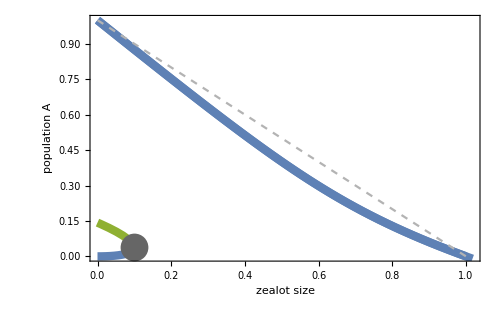

```mathematica
ratio=2;
strength=1;
params={aA->a,aB->a,dA->d vA,dB->d vB,rA->r vA,rB->r vB,bA->r vA,bB->r vB,q->ratio};
values={a->0.0,d->0,r->strength,vA->1,vB->1};

eb=EquilibriumBranches[sysCI2EqZealotSym/.(params/.values),z];
stableBranches=List[];
saddleBranches=List[];
bifPointZValue=If[ratio<1.001,2/5+0.000001,bifPintCIzealotAsym/.{r->strength,q->ratio}];
bifPoint={bifPointZValue,Re[fixedPointsCIzealotsAsym[[3]][[1,2]]/.{r->strength,q->ratio,z->bifPointZValue}]};
Do[
If[branch[[2]]==Symbol["Stable"],
AppendTo[stableBranches,branch]];
If[branch[[2]]==Symbol["Saddle"],
AppendTo[saddleBranches,branch]];
,{branch,eb[[1]]}];
Print["Found "<>ToString[Length[stableBranches]]<>" stable branches and "<>ToString[Length[saddleBranches]]<>" saddle branches"]
plt=Show[
ListLinePlot[Table[stableBranches[[sb]][[4]][[All,{3,1}]],{sb,Range[1,Length[stableBranches]]}],PlotStyle->Directive[{colours[[1]],Thickness[lineThickness]}]],
ListLinePlot[saddleBranches[[1]][[4]][[All,{3,1}]],PlotStyle->{colours[[3]],Thickness[lineThickness]}],
Plot[1-x,{x,0,1},PlotStyle->{Dashed,GrayLevel[0.7]}],
Graphics[{
Style[Point[bifPoint],Directive[{GrayLevel[0.4],PointSize[0.04]}]]
}],
PlotRange->{0,1},ImageSize->500,Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
FrameLabel->{"zealot size","population A"}
]
```

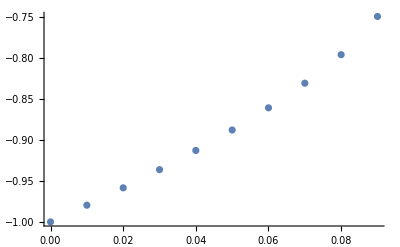

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

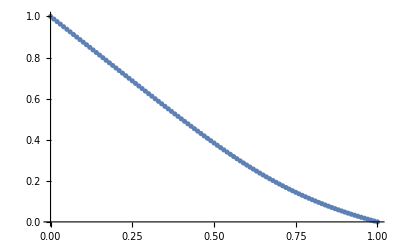

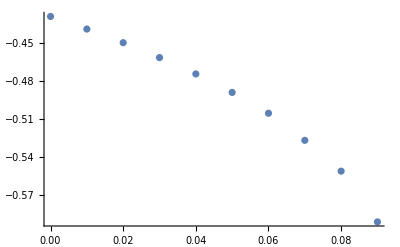

```mathematica
Do[
If[ratio==1,
limit=If[solNum>1,{0,bifPoint⟦1⟧},{bifPoint⟦1⟧,1}],
limit=If[solNum==2,{0,1},{0,bifPoint⟦1⟧}]
];
xRange=Range[limit⟦1⟧,limit⟦2⟧,0.01];
If[ratio≠1&&solNum==3,
ifunX=Interpolation[DeleteDuplicatesBy[Select[saddleBranches[[1,4]][[All,{3,1}]],#⟦1⟧≤limit⟦2⟧&],First]];
ifunY=Interpolation[DeleteDuplicatesBy[Select[saddleBranches[[1,4]][[All,{3,2}]],#⟦1⟧≤limit⟦2⟧&],First]];
,
ifunX=Interpolation[DeleteDuplicatesBy[Select[stableBranches[[solNum,4]][[All,{3,1}]],#⟦1⟧≤limit⟦2⟧&],First]];
ifunY=Interpolation[DeleteDuplicatesBy[Select[stableBranches[[solNum,4]][[All,{3,2}]],#⟦1⟧≤limit⟦2⟧&],First]];
];
finalTable=Join[Transpose[{xRange}],Transpose[{ifunX[xRange]-ifunY[xRange]}],2];
(*plt=Plot[ifunY[x],{x,limit⟦1⟧,limit⟦2⟧},Epilog->Point[DeleteDuplicatesBy[Select[stableBranches[[solNum,4]][[All,{3,2}]],#⟦1⟧≤limit⟦2⟧&],First]]];
Print[plt];*)
Export["/Users/joefresna/Google Drive/OpenMatter/Eliseo/data_sym_breaking/bifurcation_CI_Q"<>StringReplace[ToString[ratio],"."->""]<>"_P"<>ToString[solNum]<>".txt",
Block[{CForm=OutputForm@*(DecimalForm[#,15]&)},ExportString[finalTable,"Table"]]];
Print[ListPlot[finalTable]]
,{solNum,{1,2,3}}];
```

### Direct-Switch Model with Zealots

```mathematica
sysDS2EqZealotSym=DynamicalSystem[{
dA(1-A-B-z)-aA A+rA(A+z/2)(1-A-z)-rB A(B+z/2),
dB(1-A-B-z)-aB B+rB(B+z/2)(1-B-z)-rA B(A+z/2)},
{{A,-0.01,1+0.01},{B,-0.01,1+0.01}},
{{aA,0,10},{aB,0,10},{dA,0,10},{dB,0,10},{rA,0,10},{rB,0,10},{z,0,1}}]
```

DynamicalSystem[«2 ODEs»,{A,B},{aA,aB,dA,dB,rA,rB,z}]

Warning: A convergence failure occurred during continuation

Found 2 stable branches and 1 saddle branches

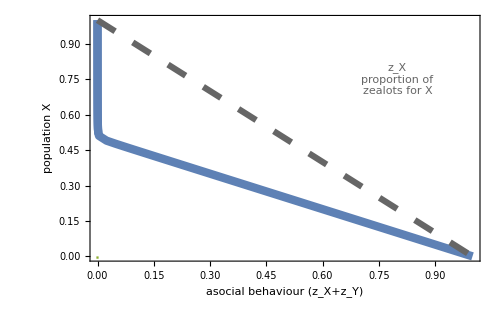

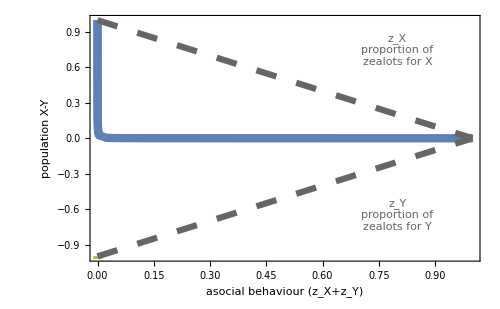

```mathematica
saveImage=False;
params={aA->a,aB->a,dA->d vA,dB->d vB,rA->r vA,rB->r vB};
ratio=1.0002;
(*ratio=2;*)
values={a->0.0,d->0,r->1,vA->1,vB->1/ratio};
eb=EquilibriumBranches[sysDS2EqZealotSym/.(params/.values),z];
stableBranchesDS=List[];
saddleBranchesDS=List[];
Do[
If[branch[[2]]==Symbol["Stable"],
AppendTo[stableBranchesDS,branch]];
If[branch[[2]]==Symbol["Saddle"],
AppendTo[saddleBranchesDS,branch]];
,{branch,eb[[1]]}];
Print["Found "<>ToString[Length[stableBranchesDS]]<>" stable branches and "<>ToString[Length[saddleBranchesDS]]<>" saddle branches"]
plt=Show[
ListLinePlot[Table[stableBranchesDS[[sb]][[4]][[All,{3,1}]],{sb,Range[1,Length[stableBranchesDS]]}],PlotStyle->Directive[{colours[[1]],Thickness[lineThickness]}]],
ListLinePlot[saddleBranchesDS[[1]][[4]][[All,{3,1}]],PlotStyle->{colours[[3]],Thickness[lineThickness]Dashing[{0.03,0.03}]}],
Plot[1-x,{x,0,1},PlotStyle->{Dashing[{0.03,0.03}],GrayLevel[0.4],Thickness[lineThickness*.75]}],
Graphics[{Style[Text["z_X\nproportion of\nzealots for X",{0.8,0.75}],Directive[{textSize,GrayLevel[0.4]}]]}],
(*Style[Text["CROSS-INHIBITION",{0.5,1.1}],Directive[{textSize,Gray},Background->White]]}],
ImagePadding->{{70,5},{50,20}},PlotRangeClipping->False,*)
Axes->False,FrameStyle->Directive[{Thickness[.005]}],
PlotRange->{0,1},ImageSize->500,Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
FrameLabel->{"asocial behaviour (z_X+z_Y)","population X"}
]
plt=Show[
ListLinePlot[Table[Join[Transpose[{stableBranchesDS[[sb]][[4]][[All,3]]}],Transpose[{stableBranchesDS[[sb]][[4]][[All,1]]-stableBranchesDS[[sb]][[4]][[All,2]]}],2],{sb,Range[1,Length[stableBranchesDS]]}],PlotStyle->Directive[{colours[[1]],Thickness[lineThickness]}]],
ListLinePlot[Join[Transpose[{saddleBranchesDS[[1]][[4]][[All,3]]}],Transpose[{saddleBranchesDS[[1]][[4]][[All,1]]-saddleBranchesDS[[1]][[4]][[All,2]]}],2],PlotStyle->{colours[[3]],Thickness[lineThickness],Dashing[{0.03,0.03}]}],
(*Plot[0,{x,0,1},PlotStyle->{colours[[3]],Thickness[lineThickness],Dashing[{0.03,0.03}]}],*)
Plot[1-x,{x,0,1},PlotStyle->{Dashing[{0.03,0.03}],GrayLevel[0.4],Thickness[lineThickness*.75]}],
Plot[-1+x,{x,0,1},PlotStyle->{Dashing[{0.03,0.03}],GrayLevel[0.4],Thickness[lineThickness*.75]}],
Graphics[{Style[Text["z_X\nproportion of\nzealots for X",{0.8,0.75}],Directive[{textSize,GrayLevel[0.4]}]],Style[Text["z_Y\nproportion of\nzealots for Y",{0.8,-0.65}],Directive[{textSize,GrayLevel[0.4]}]]}],
(*Style[Text["CROSS-INHIBITION",{0.5,1.1}],Directive[{textSize,Gray},Background->White]]}],
ImagePadding->{{70,5},{50,20}},PlotRangeClipping->False,*)
Axes->False,FrameStyle->Directive[{Thickness[.005]}],
PlotRange->{-1,1},ImageSize->500,Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
FrameLabel->{"asocial behaviour (z_X+z_Y)","population X-Y"}
]
If[saveImage&&ratio>1.001,Export[projectHomeDir<>"/SymmetryBreakingWithZealots/paperCrossInhibition/images/VM-asym"<>StringReplace[ToString[ratio],"."->""]<>"-bif.pdf",plt]];
```

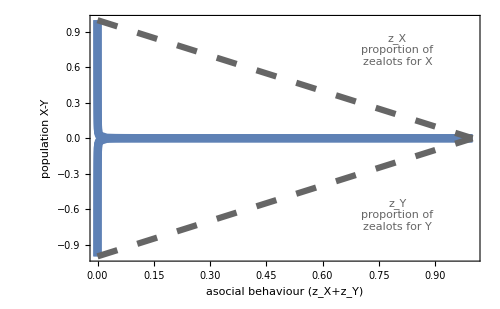

```mathematica
saveImage=False;
plt=Show[
ListLinePlot[{{0,0},{0.03,0}},PlotStyle->{colours[[3]],Thickness[lineThickness],Dashing[{0.03,0.03}]}],
ListLinePlot[Table[Join[Transpose[{stableBranchesDS[[sb]][[4]][[All,3]]}],Transpose[{stableBranchesDS[[sb]][[4]][[All,1]]-stableBranchesDS[[sb]][[4]][[All,2]]}],2],{sb,Range[1,Length[stableBranchesDS]]}],PlotStyle->Directive[{colours[[1]],Thickness[lineThickness]}]],
(*ListLinePlot[Join[Transpose[{saddleBranchesDS[[1]][[4]][[All,3]]}],Transpose[{saddleBranchesDS[[1]][[4]][[All,1]]-saddleBranchesDS[[1]][[4]][[All,2]]}],2],PlotStyle->{colours[[3]],Thickness[lineThickness],Dashing[{0.03,0.03}]}],*)
ListLinePlot[Table[Join[Transpose[{stableBranchesDS[[sb]][[4]][[All,3]]}],Transpose[{stableBranchesDS[[sb]][[4]][[All,2]]-stableBranchesDS[[sb]][[4]][[All,1]]}],2],{sb,Range[1,Length[stableBranchesDS]]}],PlotStyle->Directive[{colours[[1]],Thickness[lineThickness]}]],
(*Plot[0,{x,0,1},PlotStyle->{colours[[3]],Thickness[lineThickness],Dashing[{0.03,0.03}]}],*)
Plot[1-x,{x,0,1},PlotStyle->{Dashing[{0.03,0.03}],GrayLevel[0.4],Thickness[lineThickness*.75]}],
Plot[-1+x,{x,0,1},PlotStyle->{Dashing[{0.03,0.03}],GrayLevel[0.4],Thickness[lineThickness*.75]}],
Graphics[{Style[Text["z_X\nproportion of\nzealots for X",{0.8,0.75}],Directive[{textSize,GrayLevel[0.4]}]],Style[Text["z_Y\nproportion of\nzealots for Y",{0.8,-0.65}],Directive[{textSize,GrayLevel[0.4]}]]}],
(*Style[Text["CROSS-INHIBITION",{0.5,1.1}],Directive[{textSize,Gray},Background->White]]}],
ImagePadding->{{70,5},{50,20}},PlotRangeClipping->False,*)
Axes->False,FrameStyle->Directive[{Thickness[.005]}],
PlotRange->{-1,1},ImageSize->500,Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
FrameLabel->{"asocial behaviour (z_X+z_Y)","population X-Y"}
]
If[saveImage,Export[projectHomeDir<>"/paperCrossInhibition/images/VM-sym-bif.pdf",plt]];
```

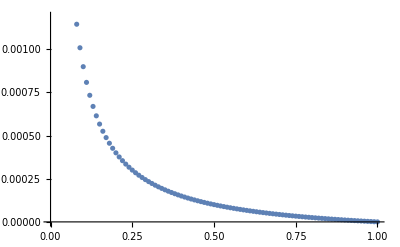

```mathematica
If[ratio<1.7,solNum=2,solNum=1];
limit={0,1};
xRange=Range[limit⟦1⟧,limit⟦2⟧,0.01];
ifunX=Interpolation[DeleteDuplicatesBy[Select[stableBranchesDS[[solNum,4]][[All,{3,1}]],#⟦1⟧≤limit⟦2⟧&],First]];
ifunY=Interpolation[DeleteDuplicatesBy[Select[stableBranchesDS[[solNum,4]][[All,{3,2}]],#⟦1⟧≤limit⟦2⟧&],First]];
finalTable=Join[Transpose[{xRange}],Transpose[{ifunX[xRange]-ifunY[xRange]}],2];
(*plt=Plot[ifunY[x],{x,limit⟦1⟧,limit⟦2⟧},Epilog->Point[DeleteDuplicatesBy[Select[stableBranches[[solNum,4]][[All,{3,2}]],#⟦1⟧≤limit⟦2⟧&],First]]];
Print[plt];*)
Export[projectHomeDir<>"/data_sym_breaking/bifurcation_DS_Q"<>StringReplace[ToString[Round[ratio,0.01]],"."->""]<>"_P"<>ToString[1]<>".txt",
Block[{CForm=OutputForm@*(DecimalForm[#,15]&)},ExportString[finalTable,"Table"]]];
Print[ListPlot[finalTable]]
```

### Cross-Inhibition with noise type 2

```mathematica
sysCI2EqNoise=DynamicalSystem[{
rA A(1-A-B)-bB A B+w(B-A),
rB B(1-A-B)-bA B A+w(A-B)},
{{A,-0.01,1+0.01},{B,-0.01,1+0.01}},
{{bA,0,10},{bB,0,10},{rA,0,10},{rB,0,10},{w,0,1}}]
```

DynamicalSystem[«2 ODEs»,{A,B},{bA,bB,rA,rB,w}]

```mathematica
sol3disap=
Solve[((-2 r^6-3 q r^6+8 q^3 r^6+9 q^4 r^6+6 q^5 r^6+2 q^6 r^6-12 r^5 w-42 q r^5 w-66 q^2 r^5 w-69 q^3 r^5 w-51 q^4 r^5 w-27 q^5 r^5 w-12 q^6 r^5 w+30 r^4 w^2+147 q r^4 w^2+288 q^2 r^4 w^2+342 q^3 r^4 w^2+249 q^4 r^4 w^2+108 q^5 r^4 w^2+24 q^6 r^4 w^2-16 r^3 w^3-102 q r^3 w^3-258 q^2 r^3 w^3-382 q^3 r^3 w^3-366 q^4 r^3 w^3-210 q^5 r^3 w^3-70 q^6 r^3 w^3)^2+4 (-(-2 r^2-q r^2-q^2 r^2+2 r w+2 q r w+2 q^2 r w)^2+3 (r^2+q r^2+q^2 r^2) (r^2-r w+2 q r w-3 q w^2-3 q^2 w^2))^3)==0,w];
Print["Computed. Now simplifying (it takes 1 min)..."];
Print[Style["The bifurcation point for cross-inhibition with direct-switch noise, for the asymmetric case is",Bold,FontSize->15,Blue]];
bifPintCInoiseAsym=FullSimplify[sol3disap⟦4⟧⟦1,2⟧]
```

Computed. Now simplifying (it takes 1 min)...

The bifurcation point for cross-inhibition with direct-switch noise, for the asymmetric case is

1/(54 q^2 (1+q) (1+q+q^2))(2 q (2+q) (1+2 q) (1+q+q^2) r-((-1+q)^2 q^2 (1+q+q^2) (92+q (304+q (423+4 q (76+23 q)))) r^2)/(-2 q^3 (-1+q^3)^2 (292+q (1770+q (4629+q (6301+q (4629+2 q (885+146 q)))))) r^3+27 √3 √((-1+q)^4 q^6 (1+q)^2 (1+q+q^2)^3 (8+q (20+q (25+4 q (5+2 q))))^3 r^6))^(1/3)+(-2 q^3 (-1+q^3)^2 (292+q (1770+q (4629+q (6301+q (4629+2 q (885+146 q)))))) r^3+27 √3 √((-1+q)^4 q^6 (1+q)^2 (1+q+q^2)^3 (8+q (20+q (25+4 q (5+2 q))))^3 r^6))^(1/3))

Found 4 stable branches and 2 saddle branches

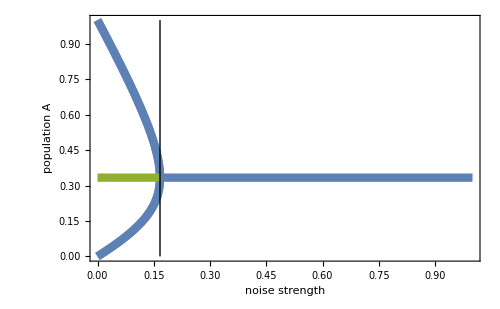

```mathematica
params={rA->r vA,rB->r vB,bA->r vA,bB->r vB};
ratio=1;
strength=1;
values={r->strength,vA->1,vB->1/ratio};

eb=EquilibriumBranches[sysCI2EqNoise/.(params/.values),w];
stableBranches=List[];
saddleBranches=List[];
Do[
If[branch[[2]]==Symbol["Stable"],
AppendTo[stableBranches,branch]];
If[branch[[2]]==Symbol["Saddle"],
AppendTo[saddleBranches,branch]];
,{branch,eb[[1]]}];
Print["Found "<>ToString[Length[stableBranches]]<>" stable branches and "<>ToString[Length[saddleBranches]]<>" saddle branches"]
plt=Show[
ListLinePlot[Table[stableBranches[[sb]][[4]][[All,{3,1}]],{sb,Range[1,Length[stableBranches]]}],PlotStyle->Directive[{colours[[1]],Thickness[lineThickness]}]],
ListLinePlot[saddleBranches[[1]][[4]][[All,{3,1}]],PlotStyle->{colours[[3]],Thickness[lineThickness]}],
Graphics[{
If[ratio==1,Line[{{1/6,0},{1/6,1}}],
Line[{{bifPintCInoiseAsym/.{r->strength,q->ratio},0},{bifPintCInoiseAsym/.{r->strength,q->ratio},1}}]]
}],
PlotRange->{{0,1},{0,1}},ImageSize->500,Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
FrameLabel->{"noise strength","population A"}
]
```

Fixed point n. 1

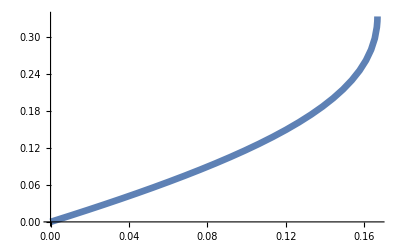

Fixed point n. 2

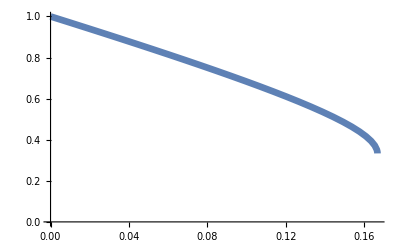

Fixed point n. 3

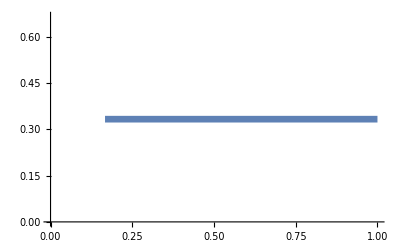

Fixed point n. 4

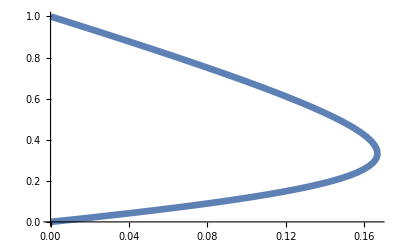

```mathematica
Do[
plt=ListLinePlot[stableBranches[[sb]][[4]][[All,{3,1}]],PlotStyle->Directive[{colours[[1]],Thickness[lineThickness]}]];
plt=ListLinePlot[Select[stableBranches[[sb,4]][[All,{3,1}]],#⟦1⟧≤limit⟦2⟧&&#⟦2⟧<=stableBranches[[4,4]][[1,1]]&],PlotStyle->Directive[{colours[[1]],Thickness[lineThickness]}]];
Print["Fixed point n. "<>ToString[sb]];
Print[plt]
,{sb,Range[1,Length[stableBranches]]}
]
```

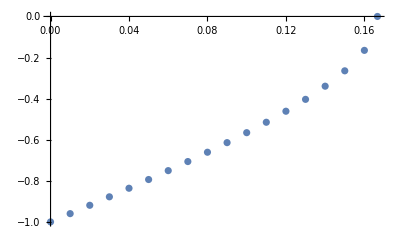

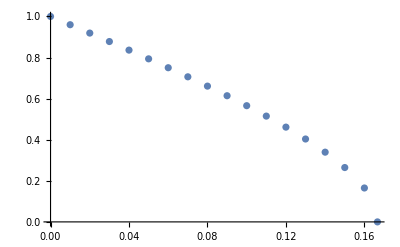

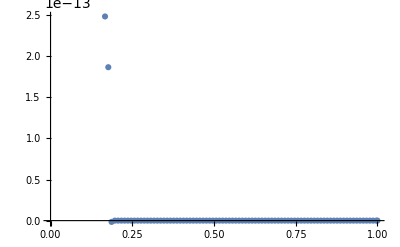

```mathematica
Do[
If[ratio==1,
(*limit=If[solNum>1,{0,bifPoint⟦1⟧},{bifPoint⟦1⟧,1}],*)
limit=If[solNum!=3,{0,1/6},{1/6,1}],
limit=If[solNum==2,{0,1},{0,bifPintCInoiseAsym/.{r->strength,q->ratio}}]
];
xRange=Range[limit⟦1⟧,limit⟦2⟧,0.01];
(* Adding final point *)
xRange=Join[xRange,{N[limit⟦2⟧]}];
If[ratio≠1&&solNum==3,
Print["TODO"];
(*ifunX=Interpolation[DeleteDuplicatesBy[Select[saddleBranches[[1,4]][[All,{3,1}]],#⟦1⟧≤limit⟦2⟧&],First]];
ifunY=Interpolation[DeleteDuplicatesBy[Select[saddleBranches[[1,4]][[All,{3,2}]],#⟦1⟧≤limit⟦2⟧&],First]];*)
,
ifunX=Interpolation[DeleteDuplicatesBy[Select[stableBranches[[solNum,4]][[All,{3,1}]],#⟦1⟧≤limit⟦2⟧&],First]];
ifunY=Interpolation[DeleteDuplicatesBy[Select[stableBranches[[solNum,4]][[All,{3,2}]],#⟦1⟧≤limit⟦2⟧&],First]];
];
finalTable=Join[Transpose[{xRange}],Transpose[{ifunX[xRange]-ifunY[xRange]}],2];
(*plt=Plot[ifunY[x],{x,limit⟦1⟧,limit⟦2⟧},Epilog->Point[DeleteDuplicatesBy[Select[stableBranches[[solNum,4]][[All,{3,2}]],#⟦1⟧≤limit⟦2⟧&],First]]];
Print[plt];*)
Export[projectHomeDir<>"/data_sym_breaking/bifurcation_CI_Q"<>StringReplace[ToString[ratio],"."->""]<>"_P"<>ToString[solNum]<>"_noise2.txt",
Block[{CForm=OutputForm@*(DecimalForm[#,15]&)},ExportString[finalTable,"Table"]]];
Print[ListPlot[finalTable]]
,{solNum,{1,2,3}}];
```

### Cross-inhibition for noise type 1 -- that is, using discovery and abandonment as (equally sized) noise

```mathematica
sysCI2EqNoiseViaU=DynamicalSystem[{
d(1-A-B)-d A+rA A(1-A-B)-bB A B+w(B-A),
d(1-A-B)-d B+rB B(1-A-B)-bA B A+w(A-B)},
{{A,-0.01,1+0.01},{B,-0.01,1+0.01}},
{{d,0,1},{bA,0,10},{bB,0,10},{rA,0,10},{rB,0,10},{w,0,1}}]
```

DynamicalSystem[«2 ODEs»,{A,B},{d,bA,bB,rA,rB,w}]

```mathematica
sol3disap=Solve[(81 d^3 q^4 r^3+81 d^3 q^5 r^3+27 d^3 q^6 r^3-27 d^2 q^2 r^4+54 d^2 q^4 r^4+27 d^2 q^5 r^4-18 d q r^5-36 d q^2 r^5-27 d q^3 r^5-9 d q^4 r^5-9 d q^5 r^5-2 r^6-3 q r^6+8 q^3 r^6+9 q^4 r^6+6 q^5 r^6+2 q^6 r^6)^2+4 (-(3 d q^2 r-2 r^2-q r^2-q^2 r^2)^2+3 (3 d^2 q^2+d q r-2 d q^2 r+r^2) (r^2+q r^2+q^2 r^2))^3==0,d];
bifPintCInoiseViaUAsym=FullSimplify[sol3disap⟦6⟧⟦1,2⟧];
```

Found 4 stable branches and 1 saddle branches

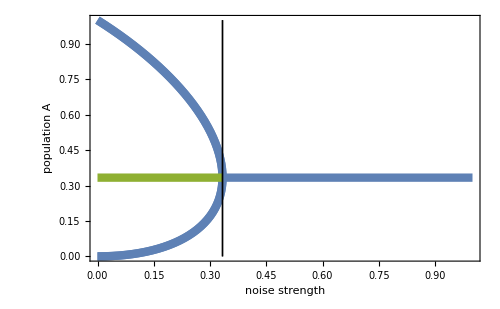

```mathematica
params={rA->r vA,rB->r vB,bA->r vA,bB->r vB,w->0};
strength=1;
ratio=1;
values={r->strength,vA->1,vB->1/ratio};

eb=EquilibriumBranches[sysCI2EqNoiseViaU/.(params/.values),d];
stableBranches=List[];
saddleBranches=List[];
Do[
If[branch[[2]]==Symbol["Stable"],
AppendTo[stableBranches,branch]];
If[branch[[2]]==Symbol["Saddle"],
AppendTo[saddleBranches,branch]];
,{branch,eb[[1]]}];
Print["Found "<>ToString[Length[stableBranches]]<>" stable branches and "<>ToString[Length[saddleBranches]]<>" saddle branches"]
plt=Show[
ListLinePlot[Table[stableBranches[[sb]][[4]][[All,{3,1}]],{sb,Range[1,Length[stableBranches]]}],PlotStyle->Directive[{colours[[1]],Thickness[lineThickness]}]],
ListLinePlot[saddleBranches[[1]][[4]][[All,{3,1}]],PlotStyle->{colours[[3]],Thickness[lineThickness]}],
Graphics[{
Line[{{1/3,0},{1/3,1}}],
Line[{{bifPintCInoiseViaUAsym/.{r->strength,q->ratio},0},{bifPintCInoiseViaUAsym/.{r->strength,q->ratio},1}}]
}],
PlotRange->{0,1},ImageSize->500,Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
FrameLabel->{"noise strength","population A"}
]
```

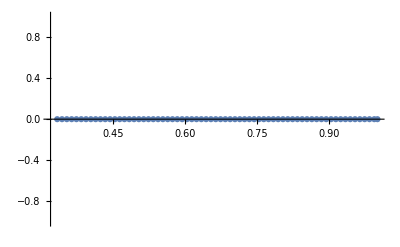

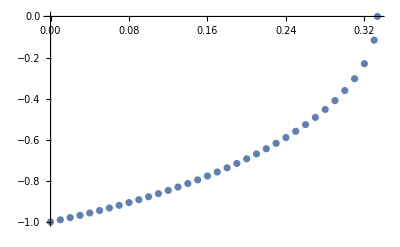

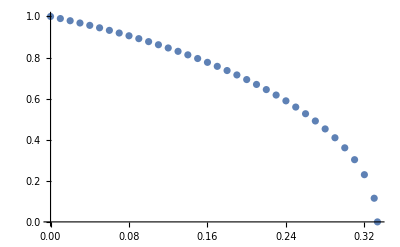

```mathematica
Do[
If[ratio==1,
(*limit=If[solNum>1,{0,bifPoint⟦1⟧},{bifPoint⟦1⟧,1}],*)
limit=If[solNum>1,{0,1/3},{1/3,1}],
limit=If[solNum==2,{0,1},{0,bifPintCInoiseViaUAsym/.{r->strength,q->ratio}}]
];
xRange=Range[limit⟦1⟧,limit⟦2⟧,0.01];
(* Adding final point *)
xRange=Join[xRange,{N[limit⟦2⟧]}];
If[ratio≠1&&solNum==3,
ifunX=Interpolation[DeleteDuplicatesBy[Select[saddleBranches[[1,4]][[All,{3,1}]],#⟦1⟧≤limit⟦2⟧&],First]];
ifunY=Interpolation[DeleteDuplicatesBy[Select[saddleBranches[[1,4]][[All,{3,2}]],#⟦1⟧≤limit⟦2⟧&],First]];
,
ifunX=Interpolation[DeleteDuplicatesBy[Select[stableBranches[[solNum,4]][[All,{3,1}]],#⟦1⟧≤limit⟦2⟧&],First]];
ifunY=Interpolation[DeleteDuplicatesBy[Select[stableBranches[[solNum,4]][[All,{3,2}]],#⟦1⟧≤limit⟦2⟧&],First]];
];
finalTable=Join[Transpose[{xRange}],Transpose[{ifunX[xRange]-ifunY[xRange]}],2];
(*plt=Plot[ifunY[x],{x,limit⟦1⟧,limit⟦2⟧},Epilog->Point[DeleteDuplicatesBy[Select[stableBranches[[solNum,4]][[All,{3,2}]],#⟦1⟧≤limit⟦2⟧&],First]]];
Print[plt];*)
Export[projectHomeDir<>"/data_sym_breaking/bifurcation_CI_Q"<>StringReplace[ToString[ratio],"."->""]<>"_P"<>ToString[solNum]<>"_noise1.txt",
Block[{CForm=OutputForm@*(DecimalForm[#,15]&)},ExportString[finalTable,"Table"]]];
Print[ListPlot[finalTable]]
,{solNum,{1,2,3}}];
```